# One-loop scalar–graviton vertex

## FORM contraction, tensor reduction, consistency checks and infrared analysis

This example uses the native FeynArts scalar model to construct the five non-vanishing one-loop, one-particle-irreducible scalar–graviton diagrams of minimally coupled Einstein gravity. The scalar potential couplings are set to zero. FeynArts supplies the routing and diagram weights. The diagrams are grouped into four contributions for the off-shell reduction and subsequent symmetry, ultraviolet and infrared analysis below.

## 1. Setup and conventions

Start with a fresh kernel and evaluate from top to bottom. FeynArts generates and draws the diagrams; FCFAConvert translates their amputated tensors to FeynCalc. FeynGravSimplify contracts the integrands with FORM, TID reduces their loop tensors, and FeynHelpers connects to Package-X for explicit scalar integrals and pole extraction. These dependencies must already be installed. The optional pure-GR bridge is not used.

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

FeynGrav 4.1.0

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

The scalar momenta p1 and p2 are incoming. FeynArts uses one outgoing graviton with momentum p1 + p2; its incoming momentum is therefore k = −p1 − p2. The loop momentum is l and the free graviton indices are μ and ν. Keep D, m and κ symbolic and use GaugeFixingEpsilon = 2. CreateFeynAmp uses PreFactor -> 1 and FCFAConvert uses Prefactor -> 1: retain the rule factors of i and native symmetry factors, without adding FeynArts’ default loop measure or its extra overall −i.

The metric signature is (+, −, −, −). The reported vertex is the amputated sum of the displayed Feynman-rule products, with their factors of i retained; it is not a separately normalized scattering matrix element.

TID uses the FeynCalc convention in which a scalar loop integral becomes i π.b2 times its PaVe function. PaXImplicitPrefactor has its default value 1: no factor (2π)^(−D) is included here. The Package-X interface expands at D = 4 − 2ε; EpsilonUV and EpsilonIR label the separated poles in that convention. These normalisations must be accounted for before comparing with a loop measure d^D l/(2π)^D.

Use the existing scalar model with an arbitrary mass. Replace the potential couplings after conversion, leaving the model parameters unassigned. Excluding its six potential field points also prevents drawing diagrams that would vanish under these replacements. The minimal scalar–graviton couplings remain present.

```mathematica
model="Single-Scalar-Tensor-Minimal-Coupling";InitializeModel[model,GenericModel->model];scalarParameters={ScalarMass->m,ScalarLambda3->0,ScalarLambda4->0};potentialVertices=Flatten[Table[FieldPoint[0]@@Join[ConstantArray[T[1],h],ConstantArray[S[1],n]],{n,3,4},{h,0,2}],1];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/Single-Scalar-Tensor-Minimal-Coupling/Single-Scalar-Tensor-Minimal-Coupling.gen

> $GenericMixing is OFF

generic model {Single-Scalar-Tensor-Minimal-Coupling} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/Single-Scalar-Tensor-Minimal-Coupling/Single-Scalar-Tensor-Minimal-Coupling.mod

> 4 particles (incl. antiparticles) in 3 classes

> $CounterTerms are ON

> 11 vertices

classes model {Single-Scalar-Tensor-Minimal-Coupling} initialized

```mathematica
masterIntegrals = {A0[__], B0[__], C0[__]};
tensorBasis = FCI[{MTD[μ, ν], FVD[p1, μ]*FVD[p2, ν], FVD[p1, ν]*FVD[p2, μ], FVD[p1, μ]*FVD[p1, ν], FVD[p2, μ]*FVD[p2, ν]}];
invariantRules = {FCI[SPD[p1, p2]] -> FCI[(1/2)*(SPD[k, k] - SPD[p1, p1] - SPD[p2, p2])]};
onShellRules = FCI[{SPD[p1, p1] -> m^2, SPD[p2, p2] -> m^2}];
collectVertex[expr_] := Collect[expr, masterIntegrals, Collect[#1, tensorBasis, Simplify] & ];
stageTimings = Association[];
SetAttributes[timed, HoldRest];
timed[label_, expr_] := Module[{measurement = AbsoluteTiming[expr]}, AssociateTo[stageTimings, label -> First[measurement]]; If[ !FreeQ[Last[measurement], _Failure | $Failed | $Aborted], Print[label, ": ", Last[measurement]]; Abort[]]; Last[measurement]];
checkStatus[value_] := Which[ !FreeQ[value, _Failure | $Failed | $Aborted], "Failure", TrueQ[value], "Passed", value === False, "Failed", True, "Unresolved"];
checks = Association[];
```

## 2. Diagram contributions

Generate one-loop 1PI topologies, excluding reducible external-leg corrections. The five retained diagrams form two triangles and three bubbles. The mass list of the complete propagator product identifies each group without relying on FeynArts’ diagram numbering. Both mixed bubbles are already included. Reduce each group separately, keeping TensorDecomposition -> False for the FORM step so that TID performs the integration.

Excluding 6 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Classes}

> Top. 1: 2 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

> Top. 5: 1 Classes insertion

Restoring 6 field point(s)

in total: 5 Classes insertions

creating amplitudes at level(s) {Classes}

> Top. 1: 2 Classes amplitudes

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 5 Classes amplitudes

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

> Top. 2 adbe/ce/dede.m, 0 diagrams

> Top. 3 adbe/cd/eded.m, 0 diagrams

> Top. 4 adbd/ce/eded.m, 0 diagrams

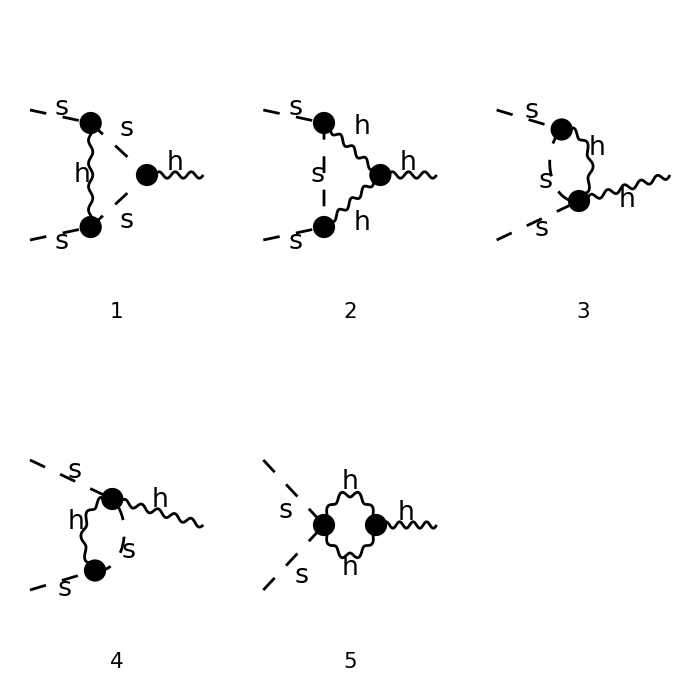

```mathematica
topologies=CreateTopologies[1,2->1,Adjacencies->{3,4,5},ExcludeTopologies->Reducible];insertions=InsertFields[topologies,{S[1],S[1]}->{T[1]},Model->model,GenericModel->model,InsertionLevel->{Classes},ExcludeFieldPoints->potentialVertices];rawAmplitudes=CreateFeynAmp[insertions,PreFactor->1,GaugeRules->{},Truncated->True,MomentumConservation->True];nativeIntegrands=FCFAConvert[rawAmplitudes,IncomingMomenta->{p1,p2},OutgoingMomenta->{p1+p2},LoopMomenta->{l},LorentzIndexNames->{μ,ν},ChangeDimension->D,Contract->False,List->True,Prefactor->1,FinalSubstitutions->scalarParameters];propagatorMasses[expr_]:=Sort[Cases[FCI[expr],PropagatorDenominator[_,mass_]:>mass,∞]];expectedMasses=Sort[{{0,0,m},{0,m,m},{0,0},{0,m},{0,m}}];If[Sort[propagatorMasses/@nativeIntegrands]=!=expectedMasses,Print["Unexpected minimal one-loop diagram inventory. Stop and inspect the model and insertions."];Abort[]];diagramSheet=Paint[insertions,ColumnsXRows->{3,2},Numbering->Simple,SheetHeader->"Minimal scalar–graviton vertex: five 1PI diagrams",AutoEdit->False,DisplayFunction->(Print/@Render[#1,ImageSize->700]&)];
```

The two-graviton bubble has weight 1/2: exchanging its two identical internal graviton lines leaves the labelled external graph unchanged. The triangles and each mixed scalar–graviton bubble have weight 1. These native weights are already in nativeIntegrands. The earlier manual V3 weight of 1 must not be retained. Saved downstream outputs, if present, predate this change and must be recalculated.

The full action also has a three-graviton–two-scalar vertex of order κ³, beyond this model’s κ² per-vertex cutoff. Closing two of its graviton legs produces a massless tadpole with a polynomial numerator and no external momentum in its denominator. It vanishes as a scaleless integral in dimensional regularisation, even for a massive external scalar. This omission is justified only with that prescription; the model does not contain the complete κ³ vertex inventory. No separate ultraviolet or infrared value is assigned to the omitted scaleless integral.

```mathematica
Grid[{{"Contribution", "Internal lines", "Native weight"},
  {"V1", "one scalar, two gravitons", 1},
  {"V2", "two scalars, one graviton", 1},
  {"V3", "two gravitons", 1/2},
  {"V4", "two mixed bubbles", "1 for each diagram"}}, Frame -> All, Alignment -> Left]
```

Contribution | Internal lines | Native weight
V1 | one scalar, two gravitons | 1
V2 | two scalars, one graviton | 1
V3 | two gravitons | 1/2
V4 | two mixed bubbles | 1 for each diagram

FORM can cancel every propagator in some numerator terms. A denominator-free polynomial is also scaleless under the declared loop integration. Remove this polynomial before TID, which otherwise leaves a loop-independent constant unchanged. This helper is specific to the present diagrams: every remaining FeynAmpDenominator depends on l.

```mathematica
reduceVertex[expr_]:=TID[expr-(expr/._FeynAmpDenominator->0),l,ToPaVe->True];
```

### 2.1. V1

Native routing: scalar l; gravitons p1 − l and p2 + l. The triangle contains two scalar–graviton vertices and one three-graviton vertex.

```mathematica
integrandV1=Total[Select[nativeIntegrands,propagatorMasses[#1]==={0,0,m}&]];
```

```mathematica
contractedV1=timed["V1: FORM",FeynGravSimplify[integrandV1,LoopMomenta->{l},TensorDecomposition->False]];reducedV1=timed["V1: TID",reduceVertex[contractedV1]];
```

```mathematica
invariantV1 = reducedV1 /. invariantRules;
𝒱1[μ_, ν_, k_, p1_, p2_, m_] = timed["V1: collect", collectVertex[invariantV1]];
```

### 2.2. V2

Loop routing: graviton l; scalars p1 − l and p2 + l.

```mathematica
integrandV2=Total[Select[nativeIntegrands,propagatorMasses[#1]==={0,m,m}&]];
```

```mathematica
contractedV2=timed["V2: FORM",FeynGravSimplify[integrandV2,LoopMomenta->{l},TensorDecomposition->False]];reducedV2=timed["V2: TID",reduceVertex[contractedV2]];
```

```mathematica
invariantV2 = reducedV2 /. invariantRules;
𝒱2[μ_, ν_, k_, p1_, p2_, m_] = timed["V2: collect", collectVertex[invariantV2]];
```

### 2.3. V3

Native routing: gravitons l and −p1 − p2 − l. The four-point scalar vertex joins the external scalars. The native integrand already contains the symmetry factor 1/2.

```mathematica
integrandV3=Total[Select[nativeIntegrands,propagatorMasses[#1]==={0,0}&]];
```

```mathematica
contractedV3=timed["V3: FORM",FeynGravSimplify[integrandV3,LoopMomenta->{l},TensorDecomposition->False]];reducedV3=timed["V3: TID",reduceVertex[contractedV3]];
```

```mathematica
invariantV3 = reducedV3 /. invariantRules;
𝒱3[μ_, ν_, k_, p1_, p2_, m_] = timed["V3: collect", collectVertex[invariantV3]];
```

### 2.4. V4: both mixed bubbles

FeynArts supplies both scalar-leg attachments. Their scalar loop momentum is l and their graviton momentum is p1 − l or p2 − l. The changes of integration variable l -> p1 − l and l -> p2 − l recover the previous graviton-loop-momentum routings. Both have unit weight. Sum the two native integrands once; do not add another exchanged copy.

```mathematica
integrandV4=Total[Select[nativeIntegrands,propagatorMasses[#1]==={0,m}&]];
```

```mathematica
contractedV4=timed["V4: FORM",FeynGravSimplify[integrandV4,LoopMomenta->{l},TensorDecomposition->False]];reducedV4=timed["V4: TID",reduceVertex[contractedV4]];
```

```mathematica
symmetricV4=reducedV4;
```

```mathematica
invariantV4 = symmetricV4 /. invariantRules;
𝒱4[μ_, ν_, k_, p1_, p2_, m_] = timed["V4: collect", collectVertex[invariantV4]];
```

### 2.5. Complete off-shell vertex

```mathematica
𝒱[μ_, ν_, k_, p1_, p2_, m_] = timed["Total: collect", collectVertex[𝒱1[μ, ν, k, p1, p2, m] + 𝒱2[μ, ν, k, p1, p2, m] + 𝒱3[μ, ν, k, p1, p2, m] + 𝒱4[μ, ν, k, p1, p2, m]]];
offShellVertex = 𝒱[μ, ν, k, p1, p2, m];
```

## 3. Consistency checks and poles

### 3.1. Symmetry of the graviton indices

```mathematica
checks["Graviton index symmetry"] = timed["Check: graviton indices", FeynGravSimplify[offShellVertex == 𝒱[ν, μ, k, p1, p2, m]]]
```

True

### 3.2. Exchange of the scalar legs

The triangle integrals are symmetric under exchange of their first two invariants for the mass patterns appearing here. Verify these identities before using them to compare the two vertices.

```mathematica
checks["Triangle identity: 0,m,0"] = Quiet[PaXEvaluate[C0[x, y, z, 0, m^2, 0] == C0[y, x, z, 0, m^2, 0]], PaXEvaluate::C0D0];
checks["Triangle identity: m,0,m"] = Quiet[PaXEvaluate[C0[x, y, z, m^2, 0, m^2] == C0[y, x, z, m^2, 0, m^2]], PaXEvaluate::C0D0];
triangleExchangeRules = FCI[{C0[SPD[p2], SPD[p1], SPD[k], m^2, 0, m^2] -> C0[SPD[p1], SPD[p2], SPD[k], m^2, 0, m^2], C0[SPD[p2], SPD[p1], SPD[k], 0, m^2, 0] -> C0[SPD[p1], SPD[p2], SPD[k], 0, m^2, 0]}];
scalarExchangeResidual = offShellVertex - (𝒱[μ, ν, k, p2, p1, m] /. triangleExchangeRules);
checks["Scalar exchange symmetry"] = Collect[scalarExchangeResidual, masterIntegrals, Simplify] == 0
```

True

### 3.3. On-shell longitudinal contraction

This checks k^μ V_μν ε^ν(k)=0 with the scalar legs on shell and k·ε=0. It is a specific on-shell contraction, not a derivation of an unrestricted off-shell Ward identity. Kinematic and polarisation relations are applied as local substitutions; no scalar-product assignments are left behind.

```mathematica
longitudinalVertex = timed["Check: longitudinal FORM", FeynGravSimplify[𝒱[μ, ν, -p1 - p2, p1, p2, m]*FVD[-p1 - p2, μ]*Pair[LorentzIndex[ν, D], Momentum[Polarization[k, I, Transversality -> True], D]]]];
transversalityRules = {Pair[Momentum[p1, D], Momentum[Polarization[k, I, Transversality -> True], D]] -> -Pair[Momentum[p2, D], Momentum[Polarization[k, I, Transversality -> True], D]]};
longitudinalResidual = ExpandScalarProduct[longitudinalVertex] /. invariantRules /. onShellRules /. transversalityRules;
checks["On-shell longitudinal contraction"] = Collect[longitudinalResidual, masterIntegrals, Simplify] == 0
```

True

### 3.4. Off-shell infrared poles

Test the generic off-shell massive vertex for IR poles. This statement is separate from the on-shell small-momentum expansion in Section 4; absence of a dimensional-regularisation pole does not imply analyticity at k^2=0.

```mathematica
offShellIRPole = timed["Check: IR pole", PaXEvaluateIR[offShellVertex]];
checks["Off-shell IR pole"] = offShellIRPole == 0
```

True

### 3.5. Ultraviolet pole

Extract the simple UV residue of each scalar integral with Package-X, then collect the tensor coefficients. Their regular D → 4 limit gives the pole residue; D-dimensional tensor labels are restored afterwards. The table prints the full UV-divergent part as the displayed common prefactor times the sum of five tensor structures and their coefficients. The complete expression is stored in uvDivergentPart.

```mathematica
offShellMasters = DeleteDuplicates[Cases[offShellVertex, _A0 | _B0 | _C0, Infinity]];
uvMasterRules = timed["Check: scalar UV residues", Function[integral, integral -> Simplify[EpsilonUV*PaXEvaluateUV[integral]]] /@ offShellMasters];
uvCoefficientSeries = Normal[Series[ChangeDimension[offShellVertex /. uvMasterRules, 4], {D, 4, 0}]];
checks["UV coefficients regular at D = 4"] = FreeQ[uvCoefficientSeries, D];
uvResidue = timed["Check: UV coefficient algebra", Collect[Expand[ChangeDimension[uvCoefficientSeries, D]], tensorBasis, Together]];
uvDivergentPart = uvResidue/EpsilonUV;
uvCommonPrefactor = (I*Pi^2*κ^3)/EpsilonUV;
uvTensorCoefficients = (Factor[Coefficient[Expand[uvDivergentPart/uvCommonPrefactor], #1]] & ) /@ tensorBasis;
checks["UV displayed tensor decomposition"] = Together[uvDivergentPart - uvCommonPrefactor*uvTensorCoefficients . tensorBasis] === 0;
Column[{Row[{HoldForm[Subsuperscript[V, "UV", "μν"]], " = ", uvCommonPrefactor, " ", HoldForm[Sum[Subscript[c, a]*Subsuperscript[T, a, "μν"], {a, 1, 5}]]}], Grid[Prepend[MapThread[{#1, #2} & , {tensorBasis, uvTensorCoefficients}], {"Tensor Tₐ", "Coefficient cₐ"}], Frame -> All, Alignment -> Left]}, ItemSize -> {Automatic, Automatic}]
```

V_UV^μν = (ⅈ π^2 κ^3)/ε_UV ∑_(a=1)^5 c_a T_a^μν
Tensor Tₐ | Coefficient cₐ
g^μν | 1/96 (62 k^2 m^2+5 k^2 p1^2+5 k^2 p2^2+8 k^4-60 m^4+28 m^2 p1^2+28 m^2 p2^2+30 p1^2 p2^2-13 p1^4-13 p2^4)
p1^μ p2^ν | 1/48 (-2 k^2-22 m^2-p1^2-p2^2)
p1^ν p2^μ | 1/48 (-2 k^2-22 m^2-p1^2-p2^2)
p1^μ p1^ν | 1/8 (-k^2-7 m^2+p1^2-2 p2^2)
p2^μ p2^ν | 1/8 (-k^2-7 m^2-2 p1^2+p2^2)

## 4. On-shell spacelike infrared limit

Put both scalar legs on shell, p₁.b2 = p₂.b2 = m.b2, with m > 0. For spacelike k define q = √(−k.b2) > 0. In the static frame k⁰ = 0, this is q = |𝐤|. Package-X separates UV and IR poles; removing their inverse regulators selects the finite remainder. This is not a complete renormalisation prescription. The following subsections expand scalar tensor coefficients before recombining momenta. They do not establish a complete tensor asymptotic expansion: cancellations may require subleading coefficients. The full finite expressions remain available in finiteIR.

```mathematica
onShellVertex = timed["IR: on-shell collect", Collect[offShellVertex /. onShellRules, masterIntegrals, Simplify]];
𝒱IR[μ_, ν_, k_, p1_, p2_, m_] = onShellVertex;
onShellMasters = DeleteDuplicates[Cases[onShellVertex, _A0 | _B0 | _C0, Infinity]];
irContributions = Association[Function[integral, integral -> Collect[Coefficient[onShellVertex, integral], tensorBasis, Simplify]*integral] /@ onShellMasters];
irRationalPart = Simplify[onShellVertex - Total[Values[irContributions]]];
checks["IR decomposition"] = Simplify[onShellVertex - irRationalPart - Total[Values[irContributions]]] == 0;
Grid[Prepend[List /@ Keys[irContributions], {"Scalar master integral"}], Frame -> All]
```

Scalar master integral
C_0(m^2,m^2,k^2,m^2,0,m^2)
A_0(m^2)
B_0(m^2,0,m^2)
C_0(m^2,m^2,k^2,0,m^2,0)
B_0(k^2,m^2,m^2)
B_0(k^2,0,0)

### 4.1. Explicit finite contributions

IR contributions is keyed by the scalar integral itself, so the analysis does not depend on the order of terms in a sum. The reconstruction check also keeps a possible rational remainder visible. All six finite contributions are retained in finiteIR. The inverse regulators are removed only after Package-X has separated UV and IR poles.

```mathematica
poleRemovalRules = {1/EpsilonIR -> 0, 1/EpsilonUV -> 0};
finiteIR = timed["IR: explicit finite integrals", Association[KeyValueMap[Function[{integral, term}, integral -> (PaXEvaluateUVIRSplit[term, PaXC0Expand -> True] /. poleRemovalRules /. FCI[SPD[k]] -> -q^2)], irContributions]]];
checks["No additional rational IR contribution"] = irRationalPart === 0;
triangleMassiveKey = FCI[C0[m^2, m^2, SPD[k], m^2, 0, m^2]];
triangleMasslessKey = FCI[C0[m^2, m^2, SPD[k], 0, m^2, 0]];
bubbleMasslessKey = FCI[B0[SPD[k], 0, 0]];
spacelikeLeading[expr_] := Assuming[m > 0 && q > 0 && ScaleMu > 0, Simplify[Asymptotic[expr, q -> 0]]];
combineIR[expr_] := Factor[MomentumCombine[expr] /. Momentum[p1 + p2, D] -> Momentum[-k, D]];
```

### 4.2. Other sectors after leading coefficient expansion

Keep the triangle with two massive propagators, the tadpole and the two bubbles with massive lines separate. Expand their scalar coefficients before combining momenta. The resulting tensor expressions can have a finite limit along a fixed spatial direction without a direction-independent limit. Finiteness alone does not imply analyticity. GaugeProjectorBar[μ, ν, k] is the existing longitudinal projector; no separate projector definition is needed.

(k^μ k^ν)/q^2=-(Θ̄)^μν(k),k^2=-q^2

```mathematica
regularKeys = DeleteCases[Keys[finiteIR], triangleMasslessKey | bubbleMasslessKey];
regularLimits = timed["IR: regular-sector limits", Association[Function[integral, integral -> combineIR[spacelikeLeading[finiteIR[integral]]]] /@ regularKeys]];
Grid[Prepend[KeyValueMap[{#1, #2} & , regularLimits], {"Scalar integral", "Contribution after leading coefficient expansion"}], Frame -> All, Alignment -> Left]
```

Scalar integral | Contribution after leading coefficient expansion
C_0(m^2,m^2,k^2,m^2,0,m^2) | 1/8 ⅈ π^2 κ^3 m^2 (log((π m^2)/μ^2)+ℽ+1) (p1^ν p2^μ+p1^μ p2^ν)
A_0(m^2) | -(ⅈ π^2 κ^3 m^4 k^μ k^ν (-3 log(μ^2/m^2)+3 ℽ-2+3 log(π)))/(18 q^2)
B_0(m^2,0,m^2) | (ⅈ π^2 κ^3 m^4 k^μ k^ν (log((π m^2)/μ^2)+ℽ))/(8 q^2)
B_0(k^2,m^2,m^2) | (ⅈ π^2 κ^3 m^4 k^μ k^ν (-3 log((π μ^2)/m^2)+3 ℽ-8+6 log(π)))/(72 q^2)

### 4.3. Triangle with two massless propagators

For m > 0 and k.b2 = −q.b2, q → 0 from positive values, the dilogarithm argument approaches 1. The bracket 4π.b2 + 3 log.b2(z) + 12 Li₂(z) therefore approaches 6π.b2. Apply the two elementary limits explicitly, so the calculation does not rely on a particular factorisation of Package-X output. The result below is the leading coefficient expansion followed by momentum recombination; it is not a complete componentwise tensor expansion along a specified external-momentum path.

```mathematica
dilogArgument = 1 + ((-1 + Sqrt[1 - -((4*m^2)/q^2)])*(-q^2))/(2*m^2);
dilogArgumentLimit = Limit[dilogArgument, q -> 0, Direction -> "FromAbove", Assumptions -> m > 0];
dilogBracketLimit = Limit[4*Pi^2 + 3*Log[z]^2 + 12*PolyLog[2, z], z -> 1, Direction -> "FromBelow"];
checks["Dilogarithm argument limit"] = dilogArgumentLimit == 1;
checks["Dilogarithm bracket limit"] = dilogBracketLimit == 6*Pi^2;
triangleLeadingInput = finiteIR[triangleMasslessKey] /. {Log[dilogArgument] -> 0, PolyLog[2, dilogArgument] -> Pi^2/6};
checks["Dilogarithm limit substitution"] = FreeQ[triangleLeadingInput, _PolyLog];
triangleLeading = timed["IR: massless triangle limit", combineIR[spacelikeLeading[triangleLeadingInput]]];
triangleCoefficient = Factor[triangleLeading/FCI[FVD[k, μ]*FVD[k, ν]]];
checks["Triangle displayed coefficient"] = Together[triangleLeading - triangleCoefficient*FCI[FVD[k, μ]*FVD[k, ν]]] === 0;
Column[{Row[{HoldForm[Subscript[C, "triangle"][q]], " = ", triangleCoefficient}], Row[{HoldForm[Subsuperscript[V, "triangle, shown", "μν"]], " = ", triangleLeading}]}, ItemSize -> {Automatic, Automatic}, Spacings -> {Automatic, 1}]
```

C_triangle(q) = -(7 ⅈ π^4 κ^3 m^3)/(32 q)
V_(triangle, shown)^μν = -(7 ⅈ π^4 κ^3 m^3 k^μ k^ν)/(32 q)

For k^2=-q^2, the exact identity is (k^μ k^ν)/q=-q(Θ̄)^μν(k). Here (Θ̄)^μν(k) denotes GaugeProjectorBar[μ, ν, k]. This displayed structure vanishes for q → 0 along a fixed spatial direction, while its square-root dependence remains nonanalytic.

### 4.4. Logarithmic bubble contribution

Package-X can distribute the momentum logarithm among several logarithms. Extract their combined coefficient. For each positive argument a(q)=c q^n, use n=(q a'(q))/(a(q)) and log a(q)=log c+n/2 log(q^2). The temporary symbol logK collects this common logarithm. The final expression uses log(-k^2/μ_R^2). ScaleMu is the renormalisation scale μ_R. FeynCalc displays this scale as μ in the output; its meaning is distinct from the free Lorentz index μ. Constants in the argument do not change the coefficient of the momentum logarithm.

```mathematica
bubbleLogArguments = DeleteDuplicates[Cases[finiteIR[bubbleMasslessKey], Log[arg_] /;  !FreeQ[arg, q] :> arg, Infinity]];
logDegrees = (Simplify[(q*D[#1, q])/#1] & ) /@ bubbleLogArguments;
checks["Bubble logarithms have monomial arguments"] = And @@ IntegerQ /@ logDegrees;
checks["Positive bubble-log constants"] = And @@ (TrueQ[FullSimplify[(#1 /. q -> 1) > 0, ScaleMu > 0 && m > 0]] & ) /@ bubbleLogArguments;
If[ !TrueQ[checks["Bubble logarithms have monomial arguments"]] ||  !TrueQ[checks["Positive bubble-log constants"]], Abort[]];
bubbleLogRules = MapThread[Log[#1] -> Log[#1 /. q -> 1] + (#2*logK)/2 & , {bubbleLogArguments, logDegrees}];
logCoefficient = Coefficient[Expand[finiteIR[bubbleMasslessKey] /. bubbleLogRules], logK];
logLeadingCoefficient = timed["IR: logarithm coefficient", combineIR[spacelikeLeading[logCoefficient]]];
logarithmicVertex = logLeadingCoefficient*Log[-(FCI[SPD[k]]/ScaleMu^2)];
logTensorCoefficient = Factor[logLeadingCoefficient/FCI[FVD[k, μ]*FVD[k, ν]]];
checks["Logarithmic displayed coefficient"] = Together[logLeadingCoefficient - logTensorCoefficient*FCI[FVD[k, μ]*FVD[k, ν]]] === 0;
Column[{Row[{HoldForm[Subscript[C, "log"]], " = ", logTensorCoefficient}], Row[{HoldForm[Subsuperscript[V, "log, shown", "μν"]], " = ", logarithmicVertex}]}, ItemSize -> {Automatic, Automatic}, Spacings -> {Automatic, 1}]
```

C_log = 77/96 ⅈ π^2 κ^3 m^2
V_(log, shown)^μν = 77/96 ⅈ π^2 κ^3 m^2 k^μ k^ν log(-k^2/μ^2)

This isolates the logarithmic sector. It does not establish that this sector is the only non-analytic contribution or the leading term of a complete observable.

## 5. Fourier convention and radial coefficient

For a rotationally invariant scalar function f(q), use the three-dimensional Fourier convention displayed below. Mathematica’s default FourierSinTransform includes √(2/π), so its prefactor here is √(π/2)/(2π.b2r). See Appendix B, equations (134)–(136), of the linked reference.

f̃(r)=∫(d^3 q)/(2π)^3 e^(-iq·r)f(q)=1/(2 π^2 r)∫_0^∞ dq q sin(qr) f(q)

```mathematica
Hyperlink["Latosh and Park, arXiv:2311.01756, Appendix B", "https://arxiv.org/html/2311.01756v3#A2"]
```

[Latosh and Park, arXiv:2311.01756, Appendix B](https://arxiv.org/html/2311.01756v3#A2)

Transform the scalar function f(q)=-C_log q^2 log(q^2/μ_R^2) associated with the longitudinal projector. The direction-dependent projector cannot be pulled through a tensor Fourier transform. Thus the scalar radial result below is not a full tensor transform. For r > 0, changing the renormalisation scale adds only contact terms at the origin. The calculation therefore omits that polynomial term and transforms -C_log q^2 log(q^2).

```mathematica
calculatedRadialInput = (-logTensorCoefficient)*q^2*Log[q^2];
calculatedRadialTransform = Assuming[r > 0, FullSimplify[(Sqrt[Pi/2]*FourierSinTransform[q*calculatedRadialInput, q, r])/(2*Pi^2*r)]];
Row[{HoldForm[Overscript[f, "~"][r]], " = ", calculatedRadialTransform, "    (r > 0)"}]
```

f̃(r) = -(77 ⅈ π κ^3 m^2)/(32 r^5)    (r > 0)

## 6. Results, checks and optional export

The mathematical summary below collects the UV decomposition and the displayed coefficientwise triangle and logarithmic sectors, followed by the scalar radial transform. offShellVertex contains the amputated vertex; onShellVertex and finiteIR retain the unexpanded expressions. Reconstruction checks test algebraic bookkeeping, while symmetry, pole and limit checks test the named properties. Neither category proves completeness of a tensor asymptotic expansion or a scattering observable.

```mathematica
Column[{Row[{HoldForm[Subsuperscript[V, "UV", "μν"]], " = ", uvCommonPrefactor, " ", HoldForm[Sum[Subscript[c, a]*Subsuperscript[T, a, "μν"], {a, 1, 5}]]}], Grid[Prepend[MapThread[List, {tensorBasis, uvTensorCoefficients}], {"Tensor", "UV coefficient"}], Frame -> All, Alignment -> Left], Row[{HoldForm[Subscript[C, "triangle"][q]], " = ", triangleCoefficient}], Row[{HoldForm[Subscript[C, "log"]], " = ", logTensorCoefficient}], Row[{HoldForm[Overscript[f, "~"][r]], " = ", calculatedRadialTransform, "    (r > 0)"}]}, ItemSize -> {Automatic, Automatic}, Spacings -> {Automatic, 1}]
```

V_UV^μν = (ⅈ π^2 κ^3)/ε_UV ∑_(a=1)^5 c_a T_a^μν
Tensor | UV coefficient
g^μν | 1/96 (62 k^2 m^2+5 k^2 p1^2+5 k^2 p2^2+8 k^4-60 m^4+28 m^2 p1^2+28 m^2 p2^2+30 p1^2 p2^2-13 p1^4-13 p2^4)
p1^μ p2^ν | 1/48 (-2 k^2-22 m^2-p1^2-p2^2)
p1^ν p2^μ | 1/48 (-2 k^2-22 m^2-p1^2-p2^2)
p1^μ p1^ν | 1/8 (-k^2-7 m^2+p1^2-2 p2^2)
p2^μ p2^ν | 1/8 (-k^2-7 m^2-2 p1^2+p2^2)
C_triangle(q) = -(7 ⅈ π^4 κ^3 m^3)/(32 q)
C_log = 77/96 ⅈ π^2 κ^3 m^2
f̃(r) = -(77 ⅈ π κ^3 m^2)/(32 r^5)    (r > 0)

```mathematica
checkSummary = Grid[Prepend[KeyValueMap[{If[MemberQ[{"UV displayed tensor decomposition", "IR decomposition", "Triangle displayed coefficient", "Logarithmic displayed coefficient"}, #1], "Reconstruction", "Symmetry / pole / limit"], #1, checkStatus[#2]} & , checks], {"Category", "Check", "Result"}], Frame -> All, Alignment -> Left];
checkSummary
```

Category | Check | Result
Symmetry / pole / limit | Graviton index symmetry | Passed
Symmetry / pole / limit | Triangle identity: 0,m,0 | Passed
Symmetry / pole / limit | Triangle identity: m,0,m | Passed
Symmetry / pole / limit | Scalar exchange symmetry | Passed
Symmetry / pole / limit | On-shell longitudinal contraction | Passed
Symmetry / pole / limit | Off-shell IR pole | Passed
Symmetry / pole / limit | UV coefficients regular at D = 4 | Passed
Reconstruction | UV displayed tensor decomposition | Passed
Reconstruction | IR decomposition | Passed
Symmetry / pole / limit | No additional rational IR contribution | Passed
Symmetry / pole / limit | Dilogarithm argument limit | Passed
Symmetry / pole / limit | Dilogarithm bracket limit | Passed
Symmetry / pole / limit | Dilogarithm limit substitution | Passed
Reconstruction | Triangle displayed coefficient | Passed
Symmetry / pole / limit | Bubble logarithms have monomial arguments | Passed
Symmetry / pole / limit | Positive bubble-log constants | Passed
Reconstruction | Logarithmic displayed coefficient | Passed

Optional timing details (expand to view)

```mathematica
Grid[Prepend[KeyValueMap[{#1, #2} & , stageTimings], {"Stage", "Elapsed seconds (wall clock)"}], Frame -> All, Alignment -> Left]
```

Stage | Elapsed seconds (wall clock)
V1: FORM | 0.230644
V1: TID | 4.1375
V1: collect | 2.07824
V2: FORM | 0.131804
V2: TID | 4.77296
V2: collect | 2.72849
V3: FORM | 0.177538
V3: TID | 1.19781
V3: collect | 0.084819
V4: FORM | 0.138045
V4: TID | 1.37978
V4: collect | 0.171411
Total: collect | 1.53102
Check: graviton indices | 0.010797
Check: longitudinal FORM | 2.86673
Check: IR pole | 4.96746
Check: scalar UV residues | 0.080773
Check: UV coefficient algebra | 0.152575
IR: on-shell collect | 0.757653
IR: explicit finite integrals | 6.44009
IR: regular-sector limits | 3.79531
IR: massless triangle limit | 0.072863
IR: logarithm coefficient | 0.034738

Optional export: set exportResult to True to write the off-shell vertex beside this notebook. The working directory is not changed. The default leaves existing files untouched.

```mathematica
exportResult = False;
If[TrueQ[exportResult], vertexOutputFile = FileNameJoin[{NotebookDirectory[], "VertexGamma.wl"}]; Put[offShellVertex, vertexOutputFile]; vertexOutputFile];
FCClearScalarProducts[];
```

The corresponding publications contain misprints in the UV-divergent term and infrared coefficients. Use the expressions displayed here with the normalisation in Section 1 and the coefficientwise expansion specified in Section 4. The checks above verify the stated identities; they do not establish completeness of the infrared tensor expansion.